```mathematica
(* 1: Adams-Bashforth 2 *)
```

```mathematica
p[r_,z_] := r^2-(r+3z/2 *r -z/2 );
```

```mathematica
p[r,z]
```

-r+r^2+z/2-(3 r z)/2

```mathematica
equns = Solve[p[r,z]==0,r]
```

{{r→1/4 (2+3 z-√(4+4 z+9 z^2))},{r→1/4 (2+3 z+√(4+4 z+9 z^2))}}

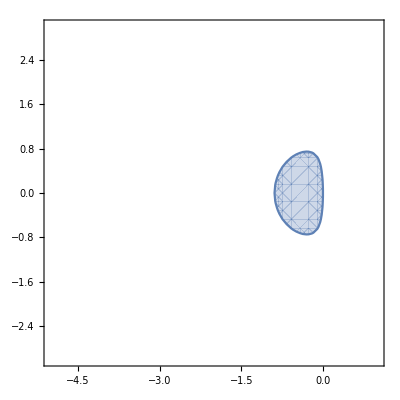

```mathematica
RegionPlot[Norm[Evaluate[r/.equns/.z->x+ⅈ y]]<1,{x,-5,1},{y,-3,3},Axes->True]
```

```mathematica
(* 2 Runge Kutta 4 *)
Clear[p,r,z];
k1[z_]:=z;
k2[z_]:=z(1+k1[z]/2);
k3[z_]:=z(1+k2[z]/2);
k4[z_] := z(1+k3[z]);
```

```mathematica
p[r_,z_]:= r - (1+1/6 * (k1[z]+2k2[z]+2k3[z]+k4[z]))
```

```mathematica
eq = Solve[p[r,z]==0,r]
```

{{r→1/24 (24+24 z+12 z^2+4 z^3+z^4)}}

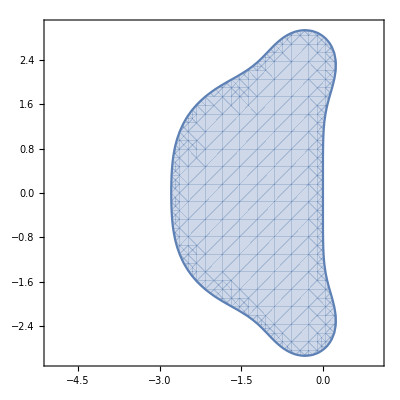

```mathematica
RegionPlot[Norm[r/.eq/.z->x+ⅈ y]<1,{x,-5,1},{y,-3,3},Axes->True]
```

```mathematica
(* 3 Backwards Euler *)
```

```mathematica
Clear[p,z,r,eq];
```

```mathematica
p[r_,z_] :=r^2 - (r+z*r^2)
```

```mathematica
eq = Solve[p[r,z]==0,r]
```

{{r→0},{r→1/(1-z)}}

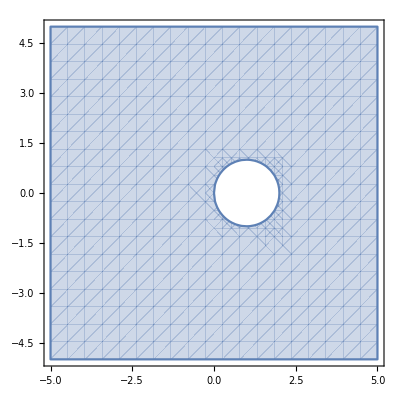

```mathematica
RegionPlot[Norm[r/.eq/.z->x+ⅈ y]<1,{x,-5,5},{y,-5,5},Axes->True]
```